# Лабораторная работа 4. Знакомство с графикой.

Выполнила студентка ММФ БГУ
 Вариант 8.  КМ, 1 к, 5 гр. Шклярик В.С.
  29 сентября 2021

## Задание 1 (Секущая прямая к заданной кривой)

Постройте функцию CurveSecant[f,x0,x1,dx], которая отображает 
заданную кривую y=f(x) и секущую по отношению к ней прямую, 
проходящую через точки с абсциссами x0<x1 из области определения функции 
y=f(x). Аргумент dx задает приращения x0-dx, x1+dx абсцисс.

```mathematica
Point[{#,f[#]}]&/@{x0,x1}
```

{Point[{x0,f[x0]}],Point[{x1,f[x1]}]}

```mathematica
Secant[f_,x0_,x1_,dx_]:=Graphics[{AbsolutePointSize[9],Hue[2/3], Point[{#,f[#]}]&/@{x0,x1},Line[{{x0-dx,(k=(f[x1]-f[x0])/(x1-x0)) (-dx)+f[x0]},{x1+dx, k (x1+dx-x0)}+f[x0]}]},Axes->True,PlotRange->{{x0-dx,x1+dx},{f[x0]-dx,f[x1]+dx}}]
```

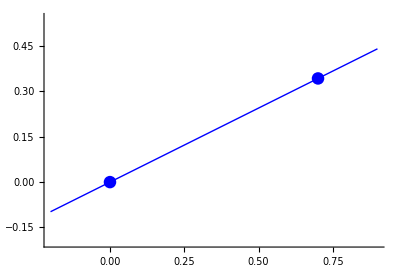

```mathematica
Secant[Power[#,3]&,0,.7,.2]
```

```mathematica
CurveSecant[f_,x0_,x1_,dx_]:=Show[Plot[f[x],{x,x0-dx,x1+dx}],Secant[f,x0,x1,dx]]
```

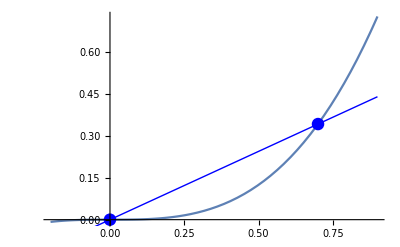

```mathematica
CurveSecant[Power[#,3]&,0,.7,.2]
```

## Задание 2 (Замкнутая ломаная)

Постройте функцию, вычисляющую графическое представление замкнутой ломаной.

```mathematica
Size=50;
P=Table[{RandomInteger[Size],RandomInteger[Size]},{RandomInteger[{3,15}]}];
```

```mathematica
BL=BreakLine[Lenght[P],P]
```

BreakLine[Lenght[{{29,18},{35,44},{20,35},{20,31},{6,3},{1,18},{25,13},{45,30},{20,50},{40,35},{29,18},{19,24},{43,30},{23,31}}],{{29,18},{35,44},{20,35},{20,31},{6,3},{1,18},{25,13},{45,30},{20,50},{40,35},{29,18},{19,24},{43,30},{23,31}}]

```mathematica
BL⟦2⟧
```

{{29,18},{35,44},{20,35},{20,31},{6,3},{1,18},{25,13},{45,30},{20,50},{40,35},{29,18},{19,24},{43,30},{23,31}}

```mathematica
Point[#]&/@BL⟦2⟧
```

{Point[{29,18}],Point[{35,44}],Point[{20,35}],Point[{20,31}],Point[{6,3}],Point[{1,18}],Point[{25,13}],Point[{45,30}],Point[{20,50}],Point[{40,35}],Point[{29,18}],Point[{19,24}],Point[{43,30}],Point[{23,31}]}

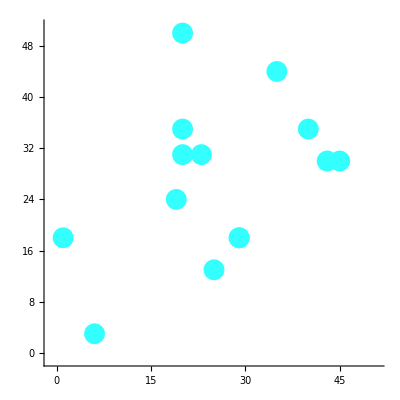

```mathematica
Fig1=Graphics[{AbsolutePointSize[15],Hue[.5,.8,1],Point[#]&/@BL⟦2⟧},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size+1}},Axes->True]
```

```mathematica
{Hue[0.051],Append[BL⟦2⟧,BL⟦2,1⟧]//Line}
```

{Hue[0.051],Line[{{29,18},{35,44},{20,35},{20,31},{6,3},{1,18},{25,13},{45,30},{20,50},{40,35},{29,18},{19,24},{43,30},{23,31},{29,18}}]}

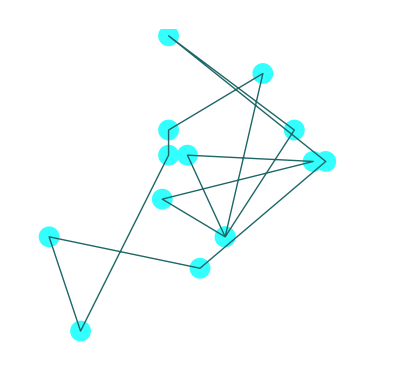

```mathematica
Fig2=Graphics[{{AbsolutePointSize[15],Hue[.5,.8,1],Point/@BL⟦2⟧},{Hue[.5,.7,.4],Append[BL⟦2⟧,BL⟦2,1⟧]//Line}},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size}}]
```

```mathematica
MapIndexed[Text[First@#2,#1]&,BL⟦2⟧]
```

{Text[1,{29,18}],Text[2,{35,44}],Text[3,{20,35}],Text[4,{20,31}],Text[5,{6,3}],Text[6,{1,18}],Text[7,{25,13}],Text[8,{45,30}],Text[9,{20,50}],Text[10,{40,35}],Text[11,{29,18}],Text[12,{19,24}],Text[13,{43,30}],Text[14,{23,31}]}

```mathematica
MapIndexed[{{Point[#1]},Text[First@#2,#1]}&,BL⟦2⟧]
```

{{{Point[{29,18}]},Text[1,{29,18}]},{{Point[{35,44}]},Text[2,{35,44}]},{{Point[{20,35}]},Text[3,{20,35}]},{{Point[{20,31}]},Text[4,{20,31}]},{{Point[{6,3}]},Text[5,{6,3}]},{{Point[{1,18}]},Text[6,{1,18}]},{{Point[{25,13}]},Text[7,{25,13}]},{{Point[{45,30}]},Text[8,{45,30}]},{{Point[{20,50}]},Text[9,{20,50}]},{{Point[{40,35}]},Text[10,{40,35}]},{{Point[{29,18}]},Text[11,{29,18}]},{{Point[{19,24}]},Text[12,{19,24}]},{{Point[{43,30}]},Text[13,{43,30}]},{{Point[{23,31}]},Text[14,{23,31}]}}

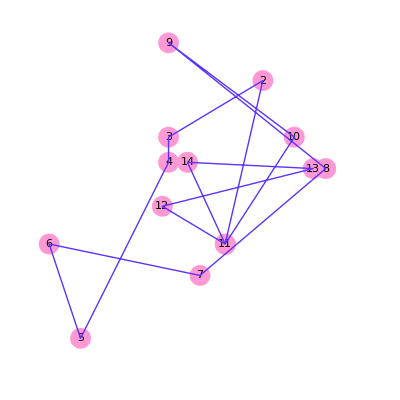

```mathematica
Fig3=Graphics[{AbsolutePointSize[15],MapIndexed[{{Hue[.9,.4,1],Point[#1]},Text[First@#2,#1]}&,BL⟦2⟧],Hue[.7,.8,1],Append[BL⟦2⟧,BL⟦2,1⟧]//Line},AspectRatio->Automatic,PlotRange->{{-1,Size+1},{-1,Size+1}}]
```

```mathematica
ClearAll[showBreakLine]
```

```mathematica
showBreakLine[BL_BreakLine]:=Graphics[{AbsolutePointSize[15],Hue[.9,.4,.1],Point[#]&/@BL⟦2⟧,Hue[.7,.8,1],Line[Append[BL⟦2⟧,BL⟦2,1⟧]],MapIndexed[{Text[First@#2,#1]}&,BL⟦2⟧]},AspectRatio->Automatic,Axes->True,PlotRange->{{-1,Max[Table[BL⟦2,i,1⟧,{i,1,Length[BL⟦2⟧]}]]+1},{-1,Max[Table[BL⟦2,i,2⟧,{i,1,Length[BL⟦2⟧]}]]+1}}]
```

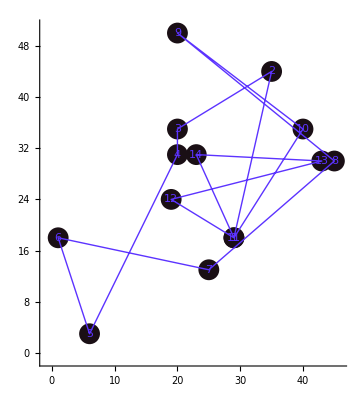

```mathematica
showBreakLine[BL]
```

## Задание 3 (График параметрической функции)

```mathematica
ParametricPlot[{Sqrt[t-3],Log[t-2]},{t,3,81}, PlotLabels->Automatic]
```

-Graphics-

```mathematica
Coordinates[n_]:=Do[Print[{N[Sqrt[t-3]], N[Log[t-2]]}],{t,3,n+2,1}]
```

```mathematica
Coordinates[11]
```

{0.,0.}

{1.,0.693147}

{1.41421,1.09861}

{1.73205,1.38629}

{2.,1.60944}

{2.23607,1.79176}

{2.44949,1.94591}

{2.64575,2.07944}

{2.82843,2.19722}

{3.,2.30259}

{3.16228,2.3979}

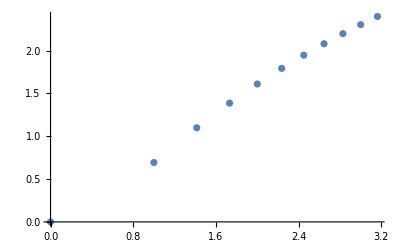

```mathematica
ListPlot[Table[{N[Sqrt[t-3]], N[Log[t-2]]},{t,3,13,1}]]
```

```mathematica
Schow[n_]:=Show[ParametricPlot[{Sqrt[t-3],Log[t-2]},{t,3,81}],ListPlot[Table[Labeled[{N[Sqrt[t-3]], N[Log[t-2]]},t],{t,3,n+2,1}]]]
```

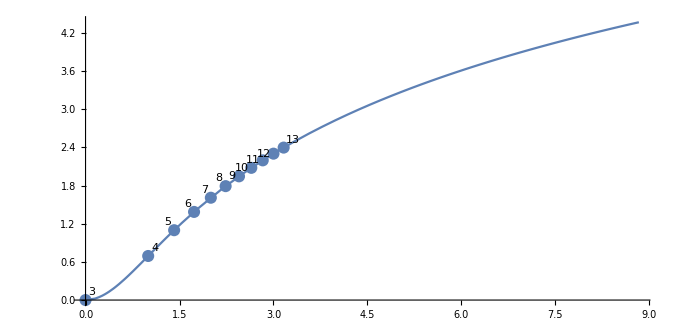

```mathematica
Schow[11]
```